```mathematica
1/2 s^(-2 n) (-s^2-u^2+s^(2 n) (1+u^2)-2 √(1-s^(2 n)) u φ-φ^2+2 s (u+√(1-s^(2 n)) φ))-(
(1-s^2)/2+s u-(1-s^(2n))/(2 s^(2n))(φ/(√(1-s^(2n)))-s+u)^2
)//FullSimplify
```

0

```mathematica
tomin=√(1-s^(2n))(s-u)-s^n √(1-2v-s^2+2 s u)/.{u->theu,v->thev}//FullSimplify
```

√(1-s^(2 n)) (s-(Q Cos[θ])/(√(1-Δ^2)))-s^n √((2 Q-(-1+s^2) (-1+Δ^2)-2 Q s √(1-Δ^2) Cos[θ]+2 Q Δ Sin[θ])/(-1+Δ^2))

```mathematica
D[tomin,θ]
```

(Q √(1-s^(2 n)) Sin[θ])/(√(1-Δ^2))-(s^n (2 Q Δ Cos[θ]+2 Q s √(1-Δ^2) Sin[θ]))/(2 (-1+Δ^2) √((2 Q-(-1+s^2) (-1+Δ^2)-2 Q s √(1-Δ^2) Cos[θ]+2 Q Δ Sin[θ])/(-1+Δ^2)))

```mathematica
Solve[(1/2 s^(-2 n) (-s^2-u^2+s^(2 n) (1+u^2)-2 √(1-s^(2 n)) u φ-φ^2+2 s (u+√(1-s^(2 n)) φ))/. u->0)==0,φ]//FullSimplify
```

{{φ→-√(-s^(2 n) (-1+s^2))+s √(1-s^(2 n))},{φ→√(-s^(2 n) (-1+s^2))+s √(1-s^(2 n))}}

```mathematica
φmax=s √(1-s^(2 n))-s^n √(1-s^2)
```

-s^n √(1-s^2)+s √(1-s^(2 n))

```mathematica
parap=(1/2 s^(-2 n) (-s^2-u^2+s^(2 n) (1+u^2)-2 √(1-s^(2 n)) u φ-φ^2+2 s (u+√(1-s^(2 n)) φ)))//FullSimplify
```

1/2 s^(-2 n) (-s^2-u^2+s^(2 n) (1+u^2)-2 √(1-s^(2 n)) u φ-φ^2+2 s (u+√(1-s^(2 n)) φ))

```mathematica
eqq1=D[thev,θ]/D[theu,θ]==D[parap,u]/.{u->theu,v->thev}//FullSimplify

eqq2=(v/.{u->theu,v->thev})==parap/.{u->theu,v->thev}//FullSimplify
```

(s^-n (√(1-Δ^2) (s-√(1-s^(2 n)) φ)-Q Cos[θ]+s^(2 n) Cot[θ] (Δ+Q Sin[θ])))/(√(1-Δ^2))==0

1/2 s^(-2 n) (s^2-s^(2 n)-2 s √(1-s^(2 n)) φ+φ^2-(2 Q (s-√(1-s^(2 n)) φ) Cos[θ])/(√(1-Δ^2))+(Q^2 (-1+s^(2 n)) Cos[θ]^2)/(-1+Δ^2))+(Q+Q Δ Sin[θ])/(1-Δ^2)==0

```mathematica
SOLO=Solve[{eqq1,eqq2},{Q,φ}];
```

```mathematica
SOLO1sim=SOLO[[1,1]]//FullSimplify
```

Q→(s^(2 n) Δ^2 Cot[θ]^2+Cos[θ] (-s √(1-Δ^2) (-s^(2 n)+(-1+s^2) (-1+Δ^2))-s^(2 n) Δ (-Δ^2+2 s^2 (-1+Δ^2)) Cot[θ])+s^(1+2 n) Δ √(1-Δ^2) Cot[θ] (2+Δ Csc[θ])-(-1+s^2+s^(2 n)) (-1+Δ^2) (1+Δ Sin[θ]))/(2 (-1+s^(2 n)) (s^2 (-1+Δ^2) Cos[θ]^2+(1+Δ Sin[θ])^2))

```mathematica
SOLO2sim=SOLO[[1,2]]//FullSimplify
```

φ→(-2 s^(2 n) Δ √(1-Δ^2) Cot[θ]+s^(1+2 n) Δ^2 (-1+Δ^2) Cot[θ]^2+Cos[θ]^2 (s (-1+Δ^2) (s^(2 n)+(1+s^2) (-1+Δ^2))-s^(2 n) Δ^3 √(1-Δ^2) Cot[θ])+2 s (-1+Δ^2) (1+Δ Sin[θ])^2-Cos[θ] (-2 s^(1+2 n) Δ (-1+Δ^2) Cot[θ]+s^(2 n) Δ^2 √(1-Δ^2) Cot[θ]^2+√(1-Δ^2) (-(-1+s^2) (-1+Δ^2) (1+Δ Sin[θ])+s^(2 n) (1+3 Δ^2+(Δ+Δ^3) Sin[θ]))))/(2 √(1-s^(2 n)) (-1+Δ^2) (s^2 (-1+Δ^2) Cos[θ]^2+(1+Δ Sin[θ])^2))

```mathematica
shouldbeφ=φ/.SOLO2sim
shouldbeQ=Q/.SOLO1sim
```

(-2 s^(2 n) Δ √(1-Δ^2) Cot[θ]+s^(1+2 n) Δ^2 (-1+Δ^2) Cot[θ]^2+Cos[θ]^2 (s (-1+Δ^2) (s^(2 n)+(1+s^2) (-1+Δ^2))-s^(2 n) Δ^3 √(1-Δ^2) Cot[θ])+2 s (-1+Δ^2) (1+Δ Sin[θ])^2-Cos[θ] (-2 s^(1+2 n) Δ (-1+Δ^2) Cot[θ]+s^(2 n) Δ^2 √(1-Δ^2) Cot[θ]^2+√(1-Δ^2) (-(-1+s^2) (-1+Δ^2) (1+Δ Sin[θ])+s^(2 n) (1+3 Δ^2+(Δ+Δ^3) Sin[θ]))))/(2 √(1-s^(2 n)) (-1+Δ^2) (s^2 (-1+Δ^2) Cos[θ]^2+(1+Δ Sin[θ])^2))

(s^(2 n) Δ^2 Cot[θ]^2+Cos[θ] (-s √(1-Δ^2) (-s^(2 n)+(-1+s^2) (-1+Δ^2))-s^(2 n) Δ (-Δ^2+2 s^2 (-1+Δ^2)) Cot[θ])+s^(1+2 n) Δ √(1-Δ^2) Cot[θ] (2+Δ Csc[θ])-(-1+s^2+s^(2 n)) (-1+Δ^2) (1+Δ Sin[θ]))/(2 (-1+s^(2 n)) (s^2 (-1+Δ^2) Cos[θ]^2+(1+Δ Sin[θ])^2))

```mathematica
Solve[eqq1/. {Q->0,φ->φmax},θ]//FullSimplify
```

{{θ→-ArcTan[(s^n Δ)/((s^(1+n)+√(1-s^2) √(1-s^(2 n))) √(1-Δ^2))]}}

```mathematica
eqq1/. {Q->Qc,φ->0}//FullSimplify
eqq2/. {Q->Qc,φ->0}//FullSimplify
```

(s^-n (s √(1-Δ^2)-Qc Cos[θ]+s^(2 n) Cot[θ] (Δ+Qc Sin[θ])))/(√(1-Δ^2))==0

1/2 s^(-2 n) (s^2-s^(2 n)+(Qc Cos[θ] (2 s √(1-Δ^2)+Qc (-1+s^(2 n)) Cos[θ]))/(-1+Δ^2))+(Qc+Qc Δ Sin[θ])/(1-Δ^2)==0

```mathematica
Solve[eqq1/. {Q->Qc,φ->0}//FullSimplify,Qc]
Solve[eqq2/. {Q->Qc,φ->0}//FullSimplify,Qc]//FullSimplify
```

{{Qc→-((s √(1-Δ^2)+s^(2 n) Δ Cot[θ]) Sec[θ])/(-1+s^(2 n))}}

{{Qc→(Sec[θ]^2 (2 s^(2 n)-2 s √(1-Δ^2) Cos[θ]-2 s^(2 n) (-Δ Sin[θ]+(-1+Δ^2) √((s^(-2 n) (-(1+s^2) (-1+Δ^2) Cos[θ]^2+s^(2 n) (Δ+Sin[θ])^2-2 s √(1-Δ^2) Cos[θ] (1+Δ Sin[θ])))/((-1+Δ^2)^2)))))/(2 (-1+s^(2 n)))},{Qc→1/(-1+s^(2 n))Sec[θ] (-s √(1-Δ^2)+s^(2 n) Sec[θ] (1-√((s^(-2 n) (-(1+s^2) (-1+Δ^2) Cos[θ]^2+s^(2 n) (Δ+Sin[θ])^2-2 s √(1-Δ^2) Cos[θ] (1+Δ Sin[θ])))/((-1+Δ^2)^2))+Δ (Sin[θ]+Δ √((s^(-2 n) (-(1+s^2) (-1+Δ^2) Cos[θ]^2+s^(2 n) (Δ+Sin[θ])^2-2 s √(1-Δ^2) Cos[θ] (1+Δ Sin[θ])))/((-1+Δ^2)^2)))))}}

```mathematica
Solve[eqq2/. {Q->Qc,φ->0}//FullSimplify,Qc]
```

{{Qc→(-1/(1-Δ^2)-(s^(1-2 n) √(1-Δ^2) Cos[θ])/(-1+Δ^2)-(Δ Sin[θ])/(1-Δ^2)-√(-4 (-1/2+1/2 s^(2-2 n)) (Cos[θ]^2/(2 (-1+Δ^2))-(s^(-2 n) Cos[θ]^2)/(2 (-1+Δ^2)))+(1/(1-Δ^2)+(s^(1-2 n) √(1-Δ^2) Cos[θ])/(-1+Δ^2)+(Δ Sin[θ])/(1-Δ^2))^2))/(2 (Cos[θ]^2/(2 (-1+Δ^2))-(s^(-2 n) Cos[θ]^2)/(2 (-1+Δ^2))))},{Qc→(-1/(1-Δ^2)-(s^(1-2 n) √(1-Δ^2) Cos[θ])/(-1+Δ^2)-(Δ Sin[θ])/(1-Δ^2)+√(-4 (-1/2+1/2 s^(2-2 n)) (Cos[θ]^2/(2 (-1+Δ^2))-(s^(-2 n) Cos[θ]^2)/(2 (-1+Δ^2)))+(1/(1-Δ^2)+(s^(1-2 n) √(1-Δ^2) Cos[θ])/(-1+Δ^2)+(Δ Sin[θ])/(1-Δ^2))^2))/(2 (Cos[θ]^2/(2 (-1+Δ^2))-(s^(-2 n) Cos[θ]^2)/(2 (-1+Δ^2))))}}

```mathematica
-4 (-1/2+1/2 s^(2-2 n)) (Cos[θ]^2/(2 (-1+Δ^2))-(s^(-2 n) Cos[θ]^2)/(2 (-1+Δ^2)))+(1/(1-Δ^2)+(s^(1-2 n) √(1-Δ^2) Cos[θ])/(-1+Δ^2)+(Δ Sin[θ])/(1-Δ^2))^2==0//FullSimplify
```

(s^-n (-(1+s^2) (-1+Δ^2) Cos[θ]^2+s^(2 n) (Δ+Sin[θ])^2-2 s √(1-Δ^2) Cos[θ] (1+Δ Sin[θ])))/(-1+Δ^2)==0

```mathematica
s=.7;
Δ=.24;
n=2;
Solve[-(1+s^2) (-1+Δ^2) Cos[θ]^2+s^(2 n) (Δ+Sin[θ])^2-2 s √(1-Δ^2) Cos[θ] (1+Δ Sin[θ])==0,θ]
jope=Solve[-(1+s^2) (-1+Δ^2) c^2+s^(2 n) (Δ-√(1-c^2))^2-2 s √(1-Δ^2) c (1-Δ √(1-c^2))==0,c]
jopo=Solve[((1+s^2) (1-Δ^2) c^2+s^(2 n)(1+Δ^2-c^2)-2 s √(1-Δ^2) c)^2-4 Δ^2( s √(1-Δ^2) c -s^(2 n))^2(1-c^2)==0,c]
ArcCos[c]/. jope
ArcCos[c]/. jopo
Clear[s,Δ,n]
```

{{θ→-1.40379},{θ→-0.640496},{θ→0.19853},{θ→1.29936}}

{{c→0.166226},{c→0.801799}}

{{c→0.166226},{c→0.268112},{c→0.801799},{c→0.980358}}

{1.40379,0.640496}

{1.40379,1.29936,0.640496,0.19853}

```mathematica
Solve[-(1+s^2) (-1+Δ^2) Cos[θ]^2+s^(2 n) (Δ+Sin[θ])^2-2 s √(1-Δ^2) Cos[θ] (1+Δ Sin[θ])==0,θ]
miracle=Solve[-(1+s^2) (-1+Δ^2) c^2+s^(2 n) (Δ-√(1-c^2))^2-2 s √(1-Δ^2) c (1-Δ √(1-c^2))==0,c]
```

{{θ→-ArcCos[-(s √(-(-1+Δ) (1+Δ)) (-4-4 s^2+4 s^(2 n)+4 Δ^2+4 s^2 Δ^2-8 s^(2 n) Δ^2))/(4 (1+2 s^2+s^4-2 s^(2 n)+s^(4 n)-2 s^(2+2 n)-2 Δ^2-2 s^4 Δ^2+2 s^(2 n) Δ^2+2 s^(2+2 n) Δ^2+Δ^4-2 s^2 Δ^4+s^4 Δ^4))-1/2 √((4 s^2)/((1+2 s^2+s^4-2 s^(2 n)+9+Δ^4-2 s^2 Δ^4+s^4 Δ^4)^2)+(8 s^4)/((1+2 s^2+12+Δ^4-2 s^2 Δ^4+s^4 Δ^4)^2)+36+1/1-(4 s^(2 n) Δ^2)/(1+2 s^2+12+Δ^4-2 s^2 Δ^4+s^4 Δ^4)-(4 s^2 Δ^4)/(1+2 s^2+s^4-2 s^(2 n)+9+Δ^4-2 s^2 Δ^4+s^4 Δ^4)+(4 s^(2 n) Δ^4)/(1+2 s^2+s^4-2 s^(2 n)+s^(4 n)-2 s^(2+2 n)-2 Δ^2-2 s^4 Δ^2+2 s^(2 n) Δ^2+2 s^(2+2 n) Δ^2+Δ^4-2 s^2 Δ^4+s^4 Δ^4))-1/2 √1]},{θ→ArcCos[1]},4,{θ→1},{θ→ArcCos[1]}}
 |  |  |  |

{{c→-(s √(-(-1+Δ) (1+Δ)) (-4-4 s^2+4 s^(2 n)+4 Δ^2+4 s^2 Δ^2-8 s^(2 n) Δ^2))/(4 (1+2 s^2+s^4-2 s^(2 n)+s^(4 n)-2 s^(2+2 n)-2 Δ^2-2 s^4 Δ^2+2 s^(2 n) Δ^2+2 s^(2+2 n) Δ^2+Δ^4-2 s^2 Δ^4+s^4 Δ^4))-1/2 √((4 s^2)/((1+2 s^2+s^4-2 s^(2 n)+9+Δ^4-2 s^2 Δ^4+s^4 Δ^4)^2)+(8 s^4)/((1+2 s^2+12+Δ^4-2 s^2 Δ^4+s^4 Δ^4)^2)+41+(4 s^(2 n) Δ^4)/(1+2 s^2+s^4-2 s^(2 n)+s^(4 n)-2 s^(2+2 n)-2 Δ^2-2 s^4 Δ^2+2 s^(2 n) Δ^2+2 s^(2+2 n) Δ^2+Δ^4-2 s^2 Δ^4+s^4 Δ^4))-1/2 √1},{c→1},1,{c→-(s √(-(1) 1) (-4-4 s^2+4 s^1+4 Δ^2+4 s^2 Δ^2-8 s^(2 n) Δ^2))/(4 (1+2 s^2+12+Δ^4-2 s^2 Δ^4+s^4 Δ^4))+1/2 √(1+42+1)+1/2 √1}}
 |  |  |  |

```mathematica
(miracle[[1]]/. n->2/. Δ->1/2/. s->1/2//FullSimplify)
```

{c→1/244 (-24+58 √3+15 √5-21 √15)}

-(1+s^2) (-1+Δ^2) c^2+s^(2 n) (Δ-√(1-c^2))^2-2 s √(1-Δ^2) c (1-Δ √(1-c^2))==0
(1+s^2) (1-Δ^2) c^2+s^(2 n)(1+Δ^2-c^2-2Δ √(1-c^2))-2 s √(1-Δ^2) c (1-Δ √(1-c^2))==0
(1+s^2) (1-Δ^2) c^2+s^(2 n)(1+Δ^2-c^2)-2Δ s^(2 n)√(1-c^2)-2 s √(1-Δ^2) c +2 s Δ √(1-Δ^2) c √(1-c^2)==0
(1+s^2) (1-Δ^2) c^2+s^(2 n)(1+Δ^2-c^2)-2 s √(1-Δ^2) c==2Δ( -s √(1-Δ^2) c +s^(2 n))√(1-c^2)
((1+s^2) (1-Δ^2) c^2+s^(2 n)(1+Δ^2-c^2)-2 s √(1-Δ^2) c)^2==4 Δ^2( s √(1-Δ^2) c -s^(2 n))^2(1-c^2)
((1+s^2) (1-Δ^2) c^2+s^(2 n)(1+Δ^2-c^2)-2 s √(1-Δ^2) c)^2-4 Δ^2( s √(1-Δ^2) c -s^(2 n))^2(1-c^2)==0

```mathematica
POPO=(((1+s^2) (1-Δ^2) c^2+s^(2 n)(1+Δ^2-c^2)-2 s √(1-Δ^2) c)^2-4 Δ^2( s √(1-Δ^2) c -s^(2 n))^2(1-c^2)//ExpandAll)//FullSimplify
```

-4 c s^(1+2 n) (1-Δ^2)^(3/2)+s^(4 n) (-1+Δ^2)^2+4 c^3 s √(1-Δ^2) (s^(2 n) (1-2 Δ^2)+(1+s^2) (-1+Δ^2))+c^4 (s^(4 n)+(1+s^2)^2-2 (1+s^4) Δ^2+(-1+s^2)^2 Δ^4+2 s^(2 n) (1+s^2) (-1+Δ^2))+2 c^2 (s^(4 n) (-1+Δ^2)+2 s^2 (-1+Δ^2)^2-s^(2 n) (1+s^2) (-1+Δ^4))

```mathematica
1/(4!)D[POPO,{c,4}]/. c->0//FullSimplify
1/(3!)D[POPO,{c,3}]/. c->0//FullSimplify
1/(2!)D[POPO,{c,2}]/. c->0//FullSimplify
1/(1!)D[POPO,{c,1}]/. c->0//FullSimplify
1/(0!)D[POPO,{c,0}]/. c->0//FullSimplify
```

s^(4 n)+(1+s^2)^2-2 (1+s^4) Δ^2+(-1+s^2)^2 Δ^4+2 s^(2 n) (1+s^2) (-1+Δ^2)

4 s √(1-Δ^2) (s^(2 n) (1-2 Δ^2)+(1+s^2) (-1+Δ^2))

2 s^(4 n) (-1+Δ^2)+4 s^2 (-1+Δ^2)^2-2 s^(2 n) (1+s^2) (-1+Δ^4)

-4 s^(1+2 n) (1-Δ^2)^(3/2)

s^(4 n) (-1+Δ^2)^2

{-1.15776,-0.590966,-0.216867}

{-0.344701,-0.374277}

{1. Qc Cos[θ]==2.39856+0.763129 Cot[θ],0.375912+3.81564 Qc+Qc (Cos[θ] (-4.79711+1. Qc Cos[θ])+1.52626 Sin[θ])==0}

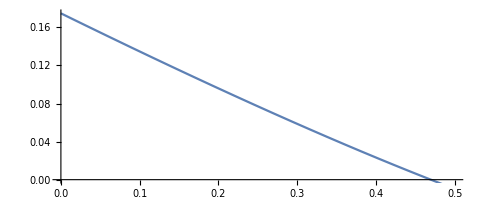

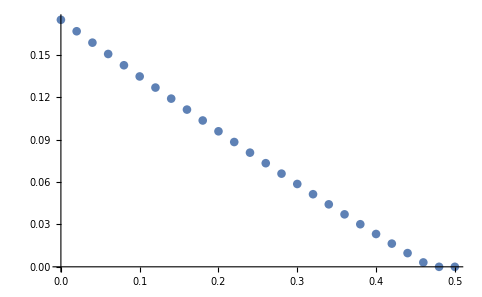

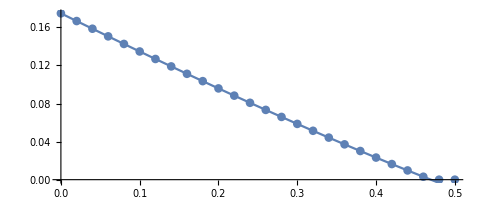

```mathematica
Δ=.4;
s=.9;
n=2;

jope=Solve[-(1+s^2) (-1+Δ^2) c^2+s^(2 n) (Δ-√(1-c^2))^2-2 s √(1-Δ^2) c (1-Δ √(1-c^2))==0,c];
-ArcCos[c]/. jope

{-ArcTan[(s^n Δ)/((s^(1+n)+√(1-s^2) √(1-s^(2 n))) √(1-Δ^2))],-ArcTan[s √(1/(1-Δ^2)-1)]}

{eqq1/. {Q->Qc,φ->0}//FullSimplify,
eqq2/. {Q->Qc,φ->0}//FullSimplify}
paraplot=ParametricPlot[{shouldbeQ,shouldbeφ},{θ,-ArcTan[Δ/(√(1-Δ^2))],-ArcTan[(s^n Δ)/((s^(1+n)+√(1-s^2) √(1-s^(2 n))) √(1-Δ^2))]},PlotRange->{{0,.5},{0,φmax}}]
numeplot=ListPlot[Table[{Q,NMinimize[{Abs[tomin],-π/2≤θ≤ 0},θ][[1]]},{Q,0,.5,.02}]]
plotillo9=Show[paraplot,numeplot]
Clear[Δ,s,n,Q]
```

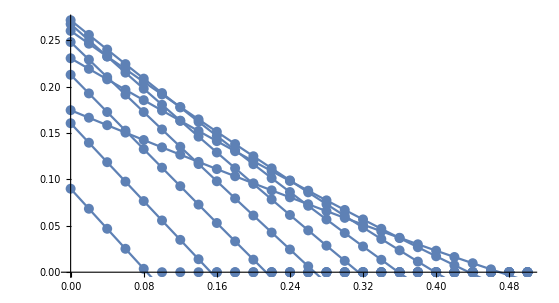

```mathematica
Show[plotillo6,plotillo7,plotillo8,plotillo9,plotillo5,plotillo4,plotillo3,plotillo2,plotillo1]
```

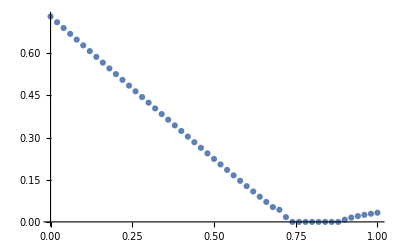

```mathematica
Δ=.4;
s=.8;
n=10;
ListPlot[Table[{Q,NMinimize[{Abs[tomin],-π/2≤θ≤ 0},θ][[1]]},{Q,0,1,.02}]]
Clear[Δ,s,n,Q]
```

{0.00125305,{θ→-0.268061}}

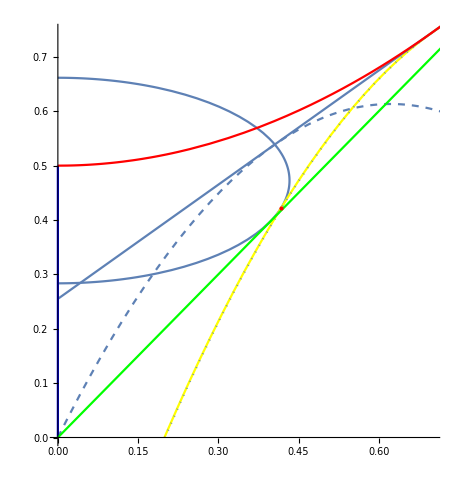

```mathematica
Δ=.4;
s=.7;
n=2;
Q=.397;

φmax=s √(1-s^(2 n))-s^n √(1-s^2)  (*  This is the max fidelity result (for Q=0) *);
themin=NMinimize[{Abs[tomin],-π/2≤θ≤ 0},θ]
poin=Graphics[{PointSize->Medium, Red,Point[{theu,thev}/.themin[[2]] ]}];
Show[ParametricPlot[{theu,thev},{θ,-π/2,π/2},PlotRange->{{0,s},{0,(1+s^2)/2}}],Plot[1/2 s^(-2 n) (-s^2-u^2+s^(2 n) (1+u^2)-2 √(1-s^(2 n)) u φ-φ^2+2 s (u+√(1-s^(2 n)) φ))/. φ-> themin[[1]],{u,0,1},PlotRange->{0,1},AspectRatio->1,PlotStyle->Yellow],Plot[1/2 s^(-2 n) (-s^2-u^2+s^(2 n) (1+u^2)-2 √(1-s^(2 n)) u φ-φ^2+2 s (u+√(1-s^(2 n)) φ))/. φ-> φmax,{u,0,1},PlotRange->{0,1},AspectRatio->1,PlotStyle->Dashed],Plot[1/2 s^(-2 n) (-s^2-u^2+s^(2 n) (1+u^2)-2 √(1-s^(2 n)) u φ-φ^2+2 s (u+√(1-s^(2 n)) φ))/. φ->0,{u,0,1},PlotRange->{0,1},AspectRatio->1,PlotStyle->Dotted](*,Region*),Plot[(1-s^2)/2+s u,{u,0,1}],Region,poin]
Clear[Δ,s,n,Q,φmax]
```

```mathematica
(s^(2 n) Sin[ϕ]^2 Cot[θ]^2+Cos[θ] (-s Cos[ϕ] (-s^(2 n)+(1-s^2)Cos[ϕ]^2)+s^(2 n) Sin[ϕ] (Sin[ϕ]^2+2 s^2 Cos[ϕ]^2) Cot[θ])+s^(1+2 n)Sin[ϕ]Cos[ϕ] Cot[θ] (2+Δ Csc[θ])-(1-s^2-s^(2 n)) Cos[ϕ]^2 (1+Sin[ϕ] Sin[θ]))/(-2 (1-s^(2 n)) ((1+Sin[ϕ] Sin[θ])^2-s^2 Cos[ϕ]^2 Cos[θ]^2))//FullSimplify
```

((-1+s^2) Cos[ϕ]^2 (1+s Cos[θ] Cos[ϕ]+Sin[θ] Sin[ϕ])+s^(2 n) Csc[θ] (Cos[ϕ] (s Cos[θ]+Cos[ϕ]) Sin[θ]+Cos[ϕ] (2 s Cos[θ] (1+s Cos[θ] Cos[ϕ])+s Δ Cot[θ]+Cos[ϕ] Sin[θ]^2) Sin[ϕ]+Cos[θ] Cot[θ] Sin[ϕ]^2+Cos[θ]^2 Sin[ϕ]^3))/(2 (-1+s^(2 n)) (-s^2 Cos[θ]^2 Cos[ϕ]^2+(1+Sin[θ] Sin[ϕ])^2))

## STUFF

```mathematica
Clear[Q,t,η1,η2]
```

```mathematica
soso=Solve[t-(s-√((-1+Q+2 (1+t^2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 t^2))/(2η1 η2)))==0 ,t]//FullSimplify
```

{{t→(s (1-Q+2 (-1+s^2) η1 η2)-√(((1-2 η1)^2 ((-1+Q)^2 (-1+η1)+(-1+Q) (-1+Q s^2) η2-(-1+s^2)^2 η1 η2^2))/η2))/(1+4 η1 (-1+η1+s^2 η2))},{t→(s (1-Q+2 (-1+s^2) η1 η2)+√(((1-2 η1)^2 ((-1+Q)^2 (-1+η1)+(-1+Q) (-1+Q s^2) η2-(-1+s^2)^2 η1 η2^2))/η2))/(1+4 η1 (-1+η1+s^2 η2))}}

```mathematica
ta=t/. soso[[1]]
tb=t/. soso[[2]]
```

(s (1-Q+2 (-1+s^2) η1 η2)-√(((1-2 η1)^2 ((-1+Q)^2 (-1+η1)+(-1+Q) (-1+Q s^2) η2-(-1+s^2)^2 η1 η2^2))/η2))/(1+4 η1 (-1+η1+s^2 η2))

(s (1-Q+2 (-1+s^2) η1 η2)+√(((1-2 η1)^2 ((-1+Q)^2 (-1+η1)+(-1+Q) (-1+Q s^2) η2-(-1+s^2)^2 η1 η2^2))/η2))/(1+4 η1 (-1+η1+s^2 η2))

```mathematica
Clear[η1,η2]
```

```mathematica
porom=Solve[((1-t^2+(-1+Q+2 (1+t^2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 t^2))/(2η1 η2))/2-(1-s^2)/2)^2==s^2 (-1+Q+2 (1+t^2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 t^2))/(2η1 η2),t]//FullSimplify
```

{{t→(s η2 (-1+Q-2 (-1+s^2) η1 η2)+√((1-2 η1)^2 η2 ((-1+Q)^2 (-1+η1)+(-1+Q) (-1+Q s^2) η2-(-1+s^2)^2 η1 η2^2)))/(η2 (1+4 η1 (-1+η1+s^2 η2)))},{t→(s η2 (-1+Q-2 (-1+s^2) η1 η2)-√((1-2 η1)^2 η2 ((-1+Q)^2 (-1+η1)+(-1+Q) (-1+Q s^2) η2-(-1+s^2)^2 η1 η2^2)))/(η2 (1+4 η1 (-1+η1+s^2 η2)))},{t→(s η2 (1-Q+2 (-1+s^2) η1 η2)+√((1-2 η1)^2 η2 ((-1+Q)^2 (-1+η1)+(-1+Q) (-1+Q s^2) η2-(-1+s^2)^2 η1 η2^2)))/(η2 (1+4 η1 (-1+η1+s^2 η2)))},{t→(s η2 (1-Q+2 (-1+s^2) η1 η2)-√((1-2 η1)^2 η2 ((-1+Q)^2 (-1+η1)+(-1+Q) (-1+Q s^2) η2-(-1+s^2)^2 η1 η2^2)))/(η2 (1+4 η1 (-1+η1+s^2 η2)))}}

```mathematica
Δ=.4;
s=.8;
n=2;
η1=(1-Δ)/2;η2=(1+Δ)/2;
thez=√((-1+Q+2 (1+t^2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 t^2))/(2η1 η2));Table[{Q,mmm=NMinimize[{(√(1-s^(2n))(s-thez)-√(t^2-(s-thez)^2)s^n)^2,Max[If[Q≤2η1,Abs[√(((Q-2 η1) (Q-2 η2))/(4 η1 η2))],0],ta]<t≤ 1-Q},t];mmm},{Q,0,.8,.1}]

Q=.8;
{ta,tb}

Table[{t,(√(1-s^(2n))(s-thez)-√(t^2-(s-thez)^2)s^n)^2},{t,t0=ta, t1=1-Q,(t1-t0)/10}]
Clear[Q]

Clear[Δ,s,σ,Q,φ,n]
```

{{0.,NMinimize[{(0.768375 (0.8-1.54303 √(-1.+0.4 √(1.-0.84 t^2)+0.42 (1+t^2)))-0.64 √(t^2-(0.8-1.54303 √(-1.+0.4 √(1.-0.84 t^2)+0.42 (1+t^2)))^2))^2,Max[0.973394-0.0945945 ⅈ,1.]<t≤1.},t]},{0.1,{0.0303993,{t→0.894354}}},{0.2,{0.0143322,{t→0.789329}}},{0.3,{0.00450976,{t→0.685116}}},{0.4,{0.000295321,{t→0.581996}}},{0.5,{3.08149×10^-33,{t→0.40477}}},{0.6,{1.74537×10^-18,{t→0.232487}}},{0.7,{3.45039×10^-17,{t→0.0706647}}},{0.8,NMinimize[{(0.768375 (0.8-1.54303 √(-0.2+0.4 √(0.04-0.84 t^2)+0.42 (1+t^2)))-0.64 √(t^2-(0.8-1.54303 √(-0.2+0.4 √(0.04-0.84 t^2)+0.42 (1+t^2)))^2))^2,0<t≤0.2},t]}}

{-0.0439851,0.155912}

{{-0.0439851,0.00114224+1.06595×10^-10 ⅈ},{-0.0195866,0.00052206+0.00178652 ⅈ},{0.0048119,0.000377895+0.00199267 ⅈ},{0.0292104,0.000709853+0.00148248 ⅈ},{0.0536089,0.002861},{0.0780074,0.00548893},{0.102406,0.00812446},{0.126804,0.0108321},{0.151203,0.0134545},{0.175601,0.0156304},{0.2,0.016384}}

```mathematica
Δ=.4;
s=.8;
Q=.2;
n=2;
η1=(1-Δ)/2;η2=(1+Δ)/2;
thez=√((-1+Q+2 (1+t^2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 t^2))/(2η1 η2));minimini=NMinimize[{(√(1-s^(2n))(s-thez)-√(t^2-(s-thez)^2)s^n)^2,If[Q≤2η1,√(((Q-2 η1) (Q-2 η2))/(4 η1 η2)),0]≤ t≤ 1-Q},t]
{tt=t/.minimini[[2]],zz=thez/.minimini[[2]]}

Clear[Δ,s,σ,Q,φ,n]
```

{0.0143322,{t→0.789329}}

{0.789329,0.208686}